```mathematica
f[x_]:=x^2 Sin[x]+Exp[-2 (x-1.5)];
Plot[f[x],{x,0,2 Pi},AxesLabel->{"x","f(x)"}]
```

```mathematica
Show[%,Frame->True,FrameLabel->{"Argum","Func"},GridLines->Automatic]
```

{Sin[x],Cos[x],ⅇ^(-0.5 x),Log[1+x]}

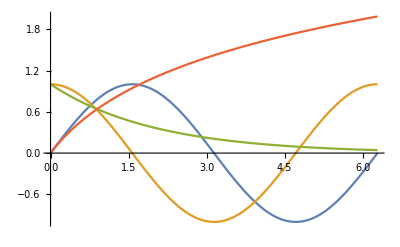

```mathematica
p={Sin[x],Cos[x],Exp[-0.5 x],Log[1+x]}
Plot[{p[[1]],p[[2]],p[[3]],p[[4]]},{x,0,2 Pi}]
```

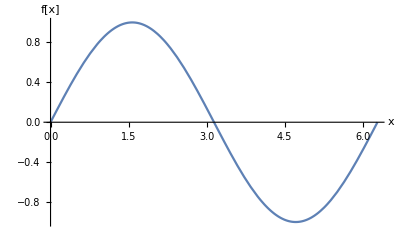
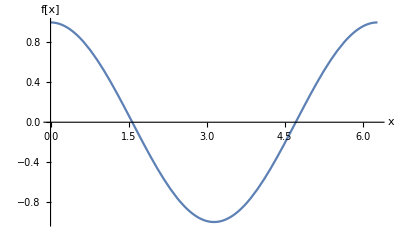
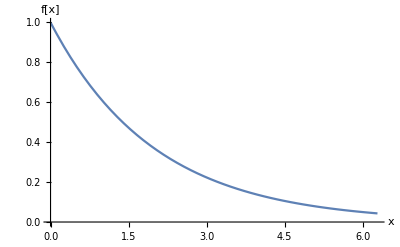
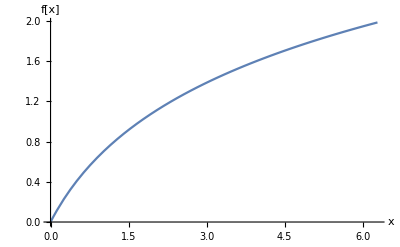

```mathematica
g=Table[Plot[p[[i]],{x,0,2 Pi},AxesLabel->{"x","f[x]"}],{i,1,4}]
```

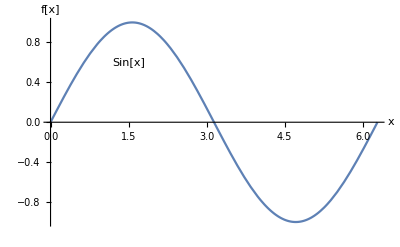
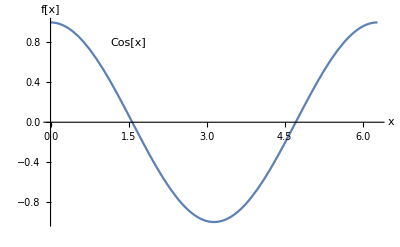
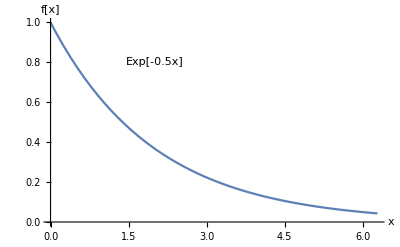
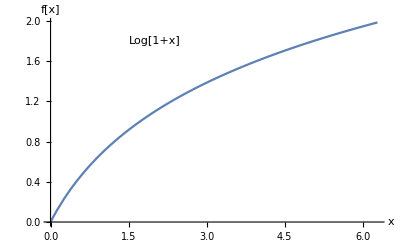

```mathematica
deskr={{1.5,0.6},{1.5,0.8},{2,0.8},{2,1.8}};
txt={"Sin[x]","Cos[x]","Exp[-0.5x]","Log[1+x]"};
g=Table[Plot[p[[i]],{x,0,2 Pi},AxesLabel->{"x","f[x]"},Epilog->Text[txt[[i]],deskr[[i]]]],{i,1,4}]
```

```mathematica
g=Table[Plot[p[[i]],{x,0,2 Pi},AxesLabel->{"x"," "},Epilog->Text[txt[[i]],deskr[[i]]],DisplayFunction->Identity],{i,1,4}];Show[GraphicsGrid[{{g[[1]],g[[2]]},{g[[3]],g[[4]]}}],Frame->True,FrameTicks->None]
```

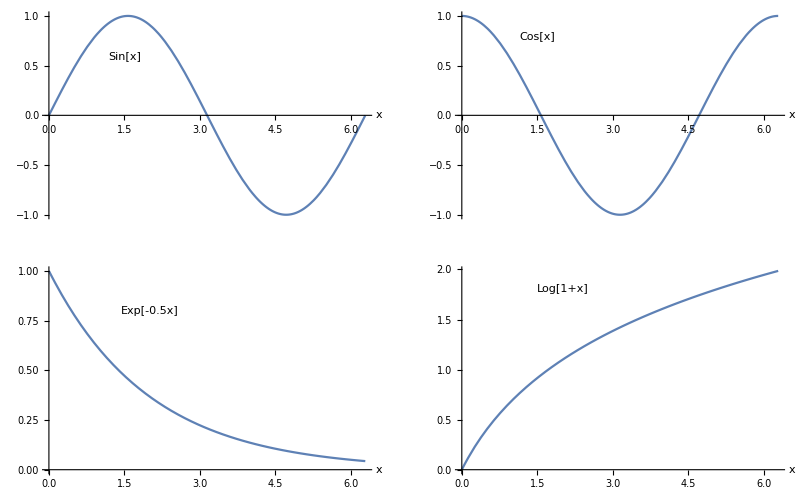

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

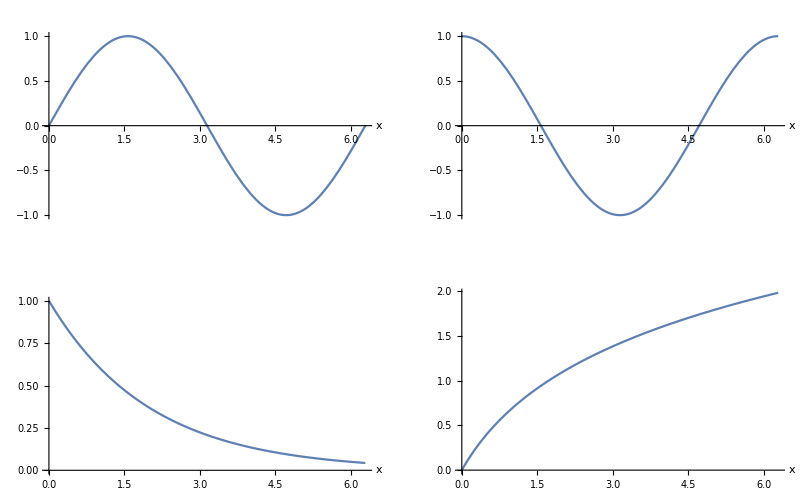

```mathematica
p={Sin[x],Cos[x],Exp[-0.5 x],Log[1+x]};
deskr={{0.1,1.3},{0.1,1.3},{0.1,1.2},{0.1,2.3}};
txt={"Sin[x]","Cos[x]","Exp[-0.5x]","Log[1+x]"};
g=Table[Plot[p[[i]],{x,0,2 Pi},AxesLabel->{"x"," "},Epilog->Text[txt[[i]],deskr[[i]]],DisplayFunction->Identity],{i,1,4}];Show[GraphicsArray[{{g[[1]],g[[2]]},{g[[3]],g[[4]]}}],Frame->True,FrameTicks->None]
```

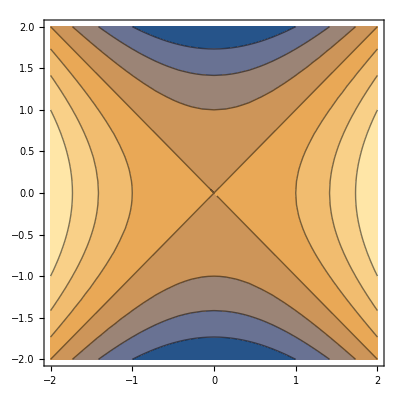

```mathematica
ContourPlot[𝑥^2−𝑦^2,{𝑥,−2,2},{𝑦,−2,2}]
```

```mathematica
Plot3D[x^2+y^2/16,{x,-2,2},{y,-4,4}]
```

```mathematica
-Graphics3D-
ParametricPlot3D[{u Sin[t],u Cos[t],t/2},{t,0,2 Pi},{u,-3,3},Ticks->None]
```

```mathematica
-Graphics3D-f2=Graphics3D[{Cuboid[{0,0,0},{1,1,3}],Cuboid[{1,0,0},{2,1,2}],Cuboid[{2,0,0},{3,1,1}]}]
Show[f2]
```

Set::write: Tag Times in (f2\\\ *Graphics3DBox[{GraphicsComplex3DBox[{{-1.34639665919603*^-6, -2.9999995714282695`, 2.2439947525641379`*^-7}, {-1.3016520711693813`, -2.702905716852157, 0.22439966759882113`}, {-2.345494711950895, -1.8704683864695497`, 0.44879911079816703`}, {-2.9247834899199505`, -0.6675619564229877, 0.6731985539975129}, {-2.924783190318551, 0.6675632690626806, 0.8975979971968588}, {-2.3454938724864105`, 1.8704694391249261`, 1.1219974403962047`}, {-1.3016508581080017`, 2.702906301031968, 1.3463968835955507`}, {-3.6739398725934315`*^-16, 2.9999995714285714`, 1.5707963267948966`}, {1.301650858108001, 2.7029063010319683`, 1.7951957699942425`}, {2.3454938724864096`, 1.8704694391249264`, 2.0195952131935884`}, {2.9247831903185504`, 0.6675632690626826, 2.243994656392934}, {2.9247834899199514`, -0.6675619564229843, 2.4683940995922797`}, {2.345494711950898, -1.870468386469546, 2.6927935427916254`}, {1.3016520711693869`, -2.7029057168521544`, 2.917192985990971}, {1.3463966610673489`*^-6, -2.9999995714282695`, 3.1415924291903177`}, {-1.1540542793108828`*^-6, -2.5714282040813736`, 2.2439947525641379`*^-7}, {-1.1157017752880412`, -2.31677632873042, 0.22439966759882113`}, {-2.010424038815053, -1.6032586169738996`, 0.44879911079816703`}, {-2.5069572770742434`, -0.5721959626482751, 0.6731985539975129}, {-2.506957020273043, 0.5721970877680119, 0.8975979971968588}, {-2.010423319274066, 1.6032595192499366`, 1.1219974403962047`}, {-1.1157007355211443`, 2.3167768294559723`, 1.3463968835955507`}, {-3.1490913193657984`*^-16, 2.5714282040816325`, 1.5707963267948966`}, {1.1157007355211437`, 2.3167768294559727`, 1.7951957699942425`}, {2.0104233192740653`, 1.6032595192499368`, 2.0195952131935884`}, {2.506957020273043, 0.5721970877680136, 2.243994656392934}, {2.506957277074244, -0.5721959626482722, 2.4683940995922797`}, {2.010424038815055, -1.6032586169738965`, 2.6927935427916254`}, {1.1157017752880458`, -2.316776328730418, 2.917192985990971}, {1.1540542809148704`*^-6, -2.5714282040813736`, 3.1415924291903177`}, {-9.617118994257356*^-7, -2.142856836734478, 2.2439947525641379`*^-7}, {-0.9297514794067009, -1.9306469406086832`, 0.22439966759882113`}, {-1.6753533656792106`, -1.3360488474782497`, 0.44879911079816703`}, {-2.089131064228536, -0.47682996887356255`, 0.6731985539975129}, {-2.089130850227536, 0.4768309064733432, 0.8975979971968588}, {-1.6753527660617216`, 1.336049599374947, 1.1219974403962047`}, {-0.9297506129342868, 1.9306473578799768`, 1.3463968835955507`}, {-2.624242766138165*^-16, 2.1428568367346936`, 1.5707963267948966`}, {0.9297506129342864, 1.930647357879977, 1.7951957699942425`}, {1.6753527660617211`, 1.3360495993749473`, 2.0195952131935884`}, {2.089130850227536, 0.47683090647334464`, 2.243994656392934}, {2.0891310642285363`, -0.47682996887356016`, 2.4683940995922797`}, {1.6753533656792128`, -1.336048847478247, 2.6927935427916254`}, {0.9297514794067048, -1.9306469406086813`, 2.917192985990971}, {9.61711900762392*^-7, -2.142856836734478, 3.1415924291903177`}, {-7.693695195405885*^-7, -1.7142854693875822`, 2.2439947525641379`*^-7}, {-0.7438011835253606, -1.5445175524869466`, 0.22439966759882113`}, {-1.3402826925433684`, -1.0688390779825996`, 0.44879911079816703`}, {-1.6713048513828286`, -0.38146397509885, 0.6731985539975129}, {-1.6713046801820286`, 0.3814647251786745, 0.8975979971968588}, Skeleton[1930]}, {{{RGBColor[Skeleton[3]], EdgeForm[Skeleton[1]], Text3DBox[FormBox[GraphicsBox[{AbsoluteThickness[Skeleton[1]], Specularity[Skeleton[2]], Skeleton[2]}], StandardForm], {{0., 0., 0.}}]}, {}, {}, {}, {}}, {{}, {}, {}, {GrayLevel[Skeleton[1]], StyleBox[{Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]]},FontColor->GrayLevel[Skeleton[1]]]}, {GrayLevel[Skeleton[1]], StyleBox[{Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]], Line3DBox[Skeleton[1]]},FontColor->GrayLevel[Skeleton[1]]]}}},VertexNormals->{{-0.16439901015616834`, 7.378210322344097*^-8, -0.9863939200236722}, {-0.1481183626250954, 0.07133011421268105, -0.9863939200236722}, {-0.10250106506435272`, 0.12853235468552934`, -0.9863939200236722}, {-0.03658218017731422, 0.16027719311807254`, -0.9863939200236722}, {0.036582252109546555`, 0.16027717670001232`, -0.9863939200236722}, {0.10250112274952826`, 0.128532308683146, -0.9863939200236722}, {0.14811839463796092`, 0.07133004773730824, -0.9863939200236722}, {0.1643990101561849, 2.0133072157076505`*^-17, -0.9863939200236722}, {0.14811839463796092`, -0.07133004773730818, -0.9863939200236722}, {0.1025011227495283, -0.128532308683146, -0.9863939200236722}, {0.03658225210954666, -0.16027717670001226`, -0.9863939200236722}, {-0.03658218017731403, -0.16027719311807254`, -0.9863939200236722}, {-0.10250106506435251`, -0.1285323546855295, -0.9863939200236722}, {-0.14811836262509526`, -0.07133011421268136, -0.9863939200236722}, {-0.16439901015616834`, -7.378210332598865*^-8, -0.9863939200236722}, {-0.19086968537592897`, 8.566211448143626*^-8, -0.9816153845598014}, {-0.17196761249227607`, 0.08281531892844356, -0.9816153845598014}, {-0.11900525447778411`, 0.1492279672252869, -0.9816153845598014}, {-0.042472452931295965`, 0.18608419475471924`, -0.9816153845598014}, {0.04247253644568297, 0.18608417569310826`, -0.9816153845598014}, {0.11900532145112715`, 0.14922791381583855`, -0.9816153845598014}, {0.17196764965968697`, 0.08281524174955125, -0.9816153845598014}, {0.19086968537594817`, 2.3374794924991732`*^-17, -0.9816153845598014}, {0.17196764965968697`, -0.08281524174955121, -0.9816153845598014}, {0.11900532145112722`, -0.14922791381583855`, -0.9816153845598014}, {0.042472536445683086`, -0.1860841756931082, -0.9816153845598014}, {-0.04247245293129576, -0.18608419475471932`, -0.9816153845598014}, {-0.11900525447778387`, -0.14922796722528708`, -0.9816153845598014}, {-0.1719676124922759, -0.0828153189284439, -0.9816153845598014}, {-0.19086968537592897`, -8.566211460049561*^-8, -0.9816153845598014}, {-0.2272296463916855, 1.0198042682599621`*^-7, -0.9738412025585584}, {-0.2047267993368332, 0.09859132737009313, -0.9738412025585584}, {-0.1416753102541117, 0.17765533671607506`, -0.9738412025585584}, {-0.05056329632417888, 0.22153253770977774`, -0.9738412025585584}, {0.050563395747744176`, 0.22153251501700114`, -0.9738412025585584}, {0.1416753899856261, 0.17765527313232662`, -0.9738412025585584}, {0.2047268435844968, 0.09859123548891056, -0.9738412025585584}, {0.2272296463917084, 2.7827605912499057`*^-17, -0.9738412025585584}, {0.20472684358449683`, -0.09859123548891051, -0.9738412025585584}, {0.14167538998562615`, -0.17765527313232662`, -0.9738412025585584}, {0.05056339574774433, -0.2215325150170011, -0.9738412025585584}, {-0.050563296324178636`, -0.22153253770977782`, -0.9738412025585584}, {-0.14167531025411143`, -0.17765533671607528`, -0.9738412025585584}, {-0.20472679933683297`, -0.09859132737009355, -0.9738412025585584}, {-0.2272296463916855, -1.0198042696773594`*^-7, -0.9738412025585584}, {-0.28000003686397645`, 1.2566372268811409`*^-7, -0.9599999892479978}, {-0.2522712694915971, 0.12148755999254401`, -0.9599999892479979}, {-0.1745770973277284, 0.2189128998767976, -0.9599999892479978}, {-0.062305799703309746`, 0.2729798673293968, -0.9599999892479979}, {0.06230592221638137, 0.2729798393665917, -0.9599999892479978}, Skeleton[1930]}], {}},Axes->True,DisplayFunction->Identity,FaceGridsStyle->Automatic,ImagePadding->Automatic,ImageSize->{11., 15.},Method->{\"DefaultGraphicsInteraction\" -> {\"Version\" -> 1.2, \"TrackMousePosition\" -> {Skeleton[2]}, \"Effects\" -> {Skeleton[3]}}},PlotRange->{{Automatic, Automatic}, {Automatic, Automatic}, {Automatic, Automatic}},PlotRangePadding->{{Scaled[0.05], Scaled[0.05]}, {Scaled[0.05], Scaled[0.05]}, {Scaled[0.05], Scaled[0.05]}},Ticks->{None, None, None},ViewPoint->{-1.060596590091722, 1.6691175287181408`, 2.7457570082605014`},ViewVertical->{0.00781525032526953, 0.9916668898318832, 0.12859121849299426`}]) is Protected.

-Graphics3D-

Show::gtype: Symbol is not a type of graphics.

Show[f2]

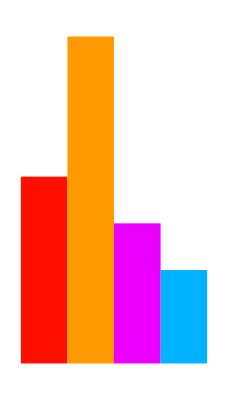

```mathematica
Show[Graphics[{Hue[.01],Rectangle[{0,0},{1,4}],Hue[.1],Rectangle[{1,0},{2,7}],Hue[.82],Rectangle[{2,0},{3,3}],Hue[.55],Rectangle[{3,0},{4,2}]}]]
```

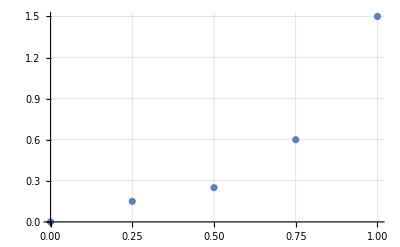

```mathematica
l=ListPlot[{{0,0},{0.25,0.15},{0.5,0.25},{0.75,0.6},{1.,1.5}},FrameLabel->{"x","f(x)"},GridLines->Automatic]
```

```mathematica
d={{0,0},{0.75,0.6},{1.,1.5},{1.5,2.5},{2.,4.}};
ind=InterpolatingPolynomial[d,x]
```

4.+(-2.+x) (2.+(0.5+(0.333333+2.89778 (-1.5+x)) (-1.+x)) x)

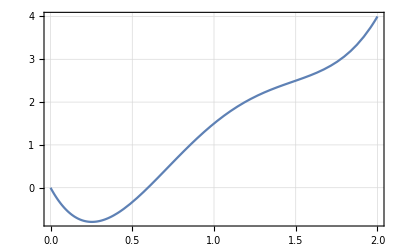

```mathematica
p1=Plot[ind,{x,0,2},Frame->True,GridLines->Automatic]
```

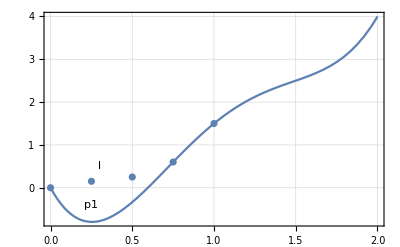

```mathematica
t=Graphics[{Text["l",{0.3,0.5}],Text["p1",{0.25,-0.4}]}];
Show[p1,l,t,Frame->True,GridLines->Automatic]
```

```mathematica
Tr1=Interpolation[d,InterpolationOrder->3]
Tr1[1.2]
```

InterpolatingFunction[…]

1.96032

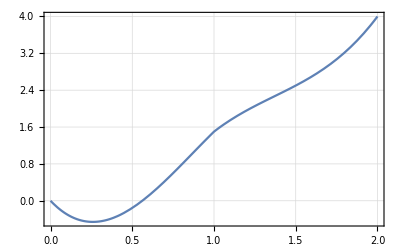

```mathematica
Plot[Tr1[x],{x,0,2.},Frame->True,GridLines->Automatic]
```

```mathematica
Plot[Evaluate[Interpolation[d]][x],{x,0,2.},Frame->True,GridLines->Automatic]
```

-Graphics-

```mathematica
NIntegrate[Tr1[x]^2,{x,0,2}]
```

7.47993

```mathematica
m={{5,2,1,0.5,-1},{0,-6,4,0.1,1},{0,2,10,1,4},{1,0,2,8,-3},{2,0,0,3,-9}};

MatrixForm[m]
```

(5 | 2 | 1 | 0.5 | -1
0 | -6 | 4 | 0.1 | 1
0 | 2 | 10 | 1 | 4
1 | 0 | 2 | 8 | -3
2 | 0 | 0 | 3 | -9)

```mathematica
b={2,-4,-3,5,8};
mi=Inverse[m];
x=mi.b
```

{0.0529219,0.46216,-0.127254,0.367172,-0.754738}

```mathematica
di=Det[mi]
```

0.0000534456

```mathematica
Е=m.mi
```

{{1.,5.20417×10^-18,0.,1.38778×10^-17,-2.77556×10^-17},{6.93889×10^-18,1.,6.245×10^-17,6.93889×10^-18,0.},{5.55112×10^-17,4.85723×10^-17,1.,8.32667×10^-17,-1.11022×10^-16},{5.55112×10^-17,2.77556×10^-17,4.16334×10^-17,1.,0.},{0.,-1.38778×10^-17,2.77556×10^-17,-5.55112×10^-17,1.}}

```mathematica
z = m.mi
```

{{1.,5.20417×10^-18,0.,1.38778×10^-17,-2.77556×10^-17},{6.93889×10^-18,1.,6.245×10^-17,6.93889×10^-18,0.},{5.55112×10^-17,4.85723×10^-17,1.,8.32667×10^-17,-1.11022×10^-16},{5.55112×10^-17,2.77556×10^-17,4.16334×10^-17,1.,0.},{0.,-1.38778×10^-17,2.77556×10^-17,-5.55112×10^-17,1.}}

```mathematica
MatrixForm[mi]
```

(0.214659 | 0.0564386 | -0.0453433 | 0.00650968 | -0.0399025
-0.00381602 | -0.147403 | 0.0616068 | -0.0113198 | 0.0151999
-0.0170705 | 0.0268832 | 0.09772 | -0.0338311 | 0.0595919
-0.00534456 | -0.0103685 | -0.0257608 | 0.152213 | -0.0627452
0.0459205 | 0.00908576 | -0.0186632 | 0.0521843 | -0.140893)

```mathematica
MatrixForm[m.mi]
```

(1. | 5.20417×10^-18 | 0. | 1.38778×10^-17 | -2.77556×10^-17
6.93889×10^-18 | 1. | 6.245×10^-17 | 6.93889×10^-18 | 0.
5.55112×10^-17 | 4.85723×10^-17 | 1. | 8.32667×10^-17 | -1.11022×10^-16
5.55112×10^-17 | 2.77556×10^-17 | 4.16334×10^-17 | 1. | 0.
0. | -1.38778×10^-17 | 2.77556×10^-17 | -5.55112×10^-17 | 1.)

```mathematica
MatrixForm[mi.m]
```

(1. | 1.249×10^-16 | 6.41848×10^-17 | 0. | 5.55112×10^-17
-3.46945×10^-18 | 1. | 3.81639×10^-17 | 2.08167×10^-17 | 0.
0. | 0. | 1. | 5.55112×10^-17 | 0.
0. | -1.38778×10^-17 | 5.55112×10^-17 | 1. | 2.22045×10^-16
5.55112×10^-17 | 6.93889×10^-18 | 2.77556×10^-17 | -1.11022×10^-16 | 1.)

```mathematica
Clear[b,d,g];
M={{а,b},{с,d}};
m={g,h};
x=LinearSolve[M,m]
```

{(d g-b h)/(-с b+а d),(с g-а h)/(с b-а d)}

```mathematica
U=Inverse[M].m
Simplify[%]
```

{(d g)/(-с b+а d)-(b h)/(-с b+а d),-(с g)/(-с b+а d)+(а h)/(-с b+а d)}

{(d g-b h)/(-с b+а d),(с g-а h)/(с b-а d)}

```mathematica
V={v1,v2};
W=M.V;
eq=W==m

Solve[eq,V]
```

{а v1+b v2,с v1+d v2}=={g,h}

{{v1→-(d g-b h)/(с b-а d),v2→-(-с g+а h)/(с b-а d)}}